### Categorization

Tutorial

EcoEvo Package

EcoEvo`

EcoEvo/tutorial/RickerModel

### Keywords

### Syntax Templates

Details

# Ricker Model

The Ricker Model is an unstructured, single-species discrete-time population model with density-dependence.  It is a discrete-time analog of logistic growth.

n is population size and r is the intrinsic rate of increase.

```mathematica
Needs["EcoEvo`"];
```

Set up the model:

```mathematica
SetModel[{ModelType->"DiscreteTime",
Pop[n]->{Equation:>n[t]*E^(r(1-n[t]))}}]
```

First, find equilibria:

```mathematica
eq=SolveEcoEq[]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{n→0},{n→1}}

Now calculate eigenvalues at these equilibria.

```mathematica
EcoEigenvalues[eq]
```

{{ⅇ^r},{1-r}}

Stability in discrete time requires the real part of eigenvalues to be between -1 and 1.  We can easily see that the trivial equilibrium {n→0} is stable if ⅇ^r<1 or equivalently r<0 and that the positive {n→1} equilibrium is stable if 0<r<2.  Let's verify with EcoStableQ:

```mathematica
EcoStableQ[eq]
```

{Which[ⅇ^Re[r]≤1.,True,ⅇ^Re[r]>1.,False,Else,Indeterminate],Which[Abs[1-r]≤1.,True,Abs[1-r]>1.,False,Else,Indeterminate]}

Let's simulate the model with varying r to see the dynamics.

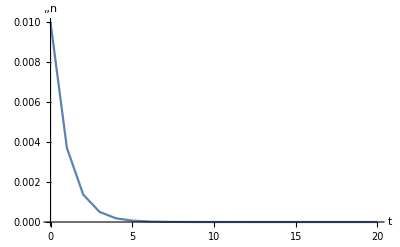

```mathematica
r=-1;
sol=EcoSim[{n->0.01},20];
PlotDynamics[sol]
```

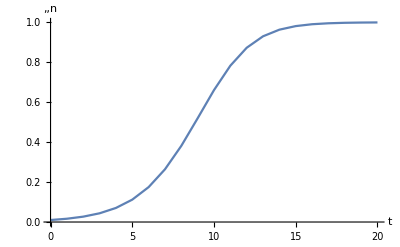

```mathematica
r=0.5;
sol=EcoSim[{n->0.01},20];
PlotDynamics[sol]
```

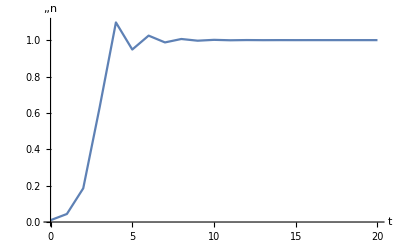

```mathematica
r=1.5;
sol=EcoSim[{n->0.01},20];
PlotDynamics[sol]
```

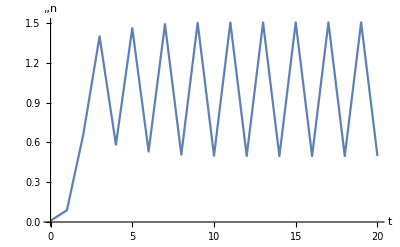

```mathematica
r=2.2;
sol=EcoSim[{n->0.01},20];
PlotDynamics[sol]
```

There is a flip (period-doubling) bifurcation at r=2 where the eigenvalue of the {n→1} equilibrium goes through -1. We can solve for the two-cycle using FindEcoCycle, then check its stability applying EcoEigenvalues to the two-cycle:

{n→TimeSeries[…]}

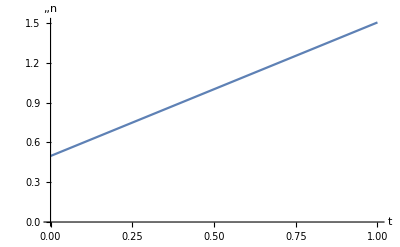

{0.215727}

```mathematica
ec=FindEcoCycle[{n->0.2},Period->2]
PlotDynamics[ec]
EcoEigenvalues[ec]
```

Increasing r leads to another period doubling bifurcation:

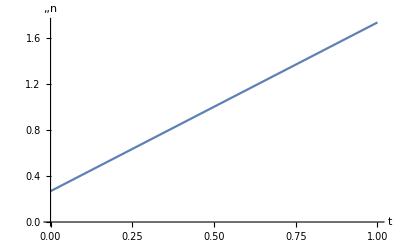

{-1.0847}

```mathematica
r=2.55;
ec=FindEcoCycle[{n->0.3911},Period->2,Method->"FindRoot"];
PlotDynamics[ec]
EcoEigenvalues[ec]
```

Let's look at the resulting four-cycle:

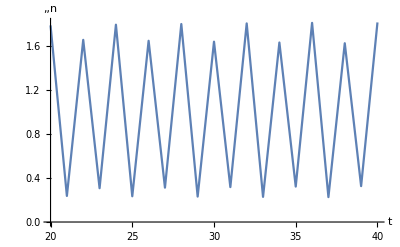

```mathematica
sol=EcoSim[{n->0.1},40];
PlotDynamics[FinalSlice[sol,20]]
```

We can find the attractor using FindEcoAttractor:

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {}. Trying EcoSim.

FindEcoAttractor::nostst: Warning: EcoSim did not find a steady state (d/dt={1.48963} at t=1000). Trying FindEcoCycle.

{n→TimeSeries[…]}

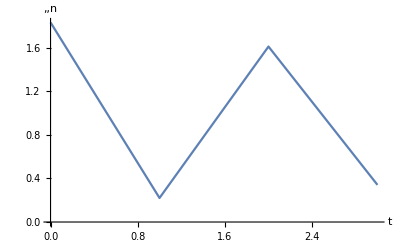

```mathematica
ec=FindEcoAttractor[{n->0.1}]
PlotDynamics[ec]
```

Here's a brute-force way to get a bifurcation diagram:

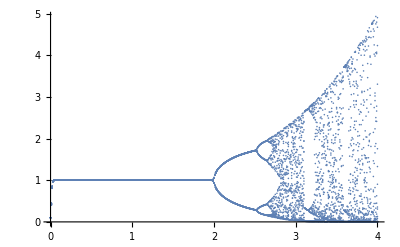

```mathematica
Clear[r];
res=Table[
sol=EcoSim[{n->0.1},200];
ReplacePart[n/.Normal[FinalSlice[sol,20]],{_,1}->r]
,{r,0.0,4.0,0.01}];ListPlot[Flatten[res,1],PlotRange->All]
```

## References

May RM. 1974. Biological populations with nonoverlapping generations: stable points, stable cycles, and chaos. Science 186: 645–647.

More About

Related Tutorials

ExampleModels

Related Wolfram Education Group Courses